```mathematica
2-2
```

0

# Site-specific Hexagonal Walks 3

Nicholas Wheeler
14 January 2012

### Introduction

Walks on this honeycomb structure

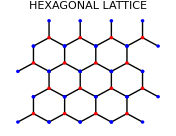

place the walker alternately on nodes of two types, ● & ●. Correspondingly, his next-step options are of two types, described by R-vectors else B-vectors

```mathematica
R1=N[{Cos[π/2],Sin[π/2]}];
R2=N[{Cos[π/2-4(2π)/12],Sin[π/2-4(2π)/12]}];
R3=N[{Cos[π/2-8(2π)/12],Sin[π/2-8(2π)/12]}];
B1=-R1;
B2=-R2;
B3=-R3;
```

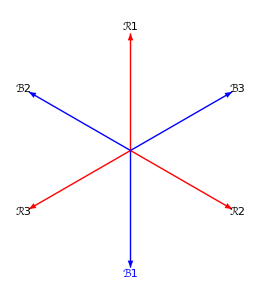

```mathematica
Graphics[{
{Thick,Red,Arrow[{{0,0},R1}]},
Text[ℛ1,1.05R1],
{Thick,Blue,Arrow[{{0,0},B3}]},
Text[ℬ3,1.05B3],
{Thick,Red,Arrow[{{0,0},R2}]},
Text[ℛ2,1.05R2],
{Thick,Blue,Arrow[{{0,0},B1}],
Text[ℬ1,1.05B1]},
{Thick,Red,Arrow[{{0,0},R3}]},
Text[ℛ3,1.05R3],
{Thick,Blue,Arrow[{{0,0},B2}]},
Text[ℬ2,1.05B2]}]
```

We are interested in walks where the next-step probabilities are "site-specific"—vary in a controlled way from site to site. 

I have been thus far unable to use off-the-shelf material to construct a command that generates such walks automatically. It is my guess, after many instructive failures, that to capture the walker's insructions—simple though they are—I would have to resort to Mathematica programming, of which I am presently ignorant. So I proceed here "by hand."

### Proof of method: construction of unbiased walks

To make next-step decisions I will make use of the weighted random choice command

RandomChoice[{w_1,w_2,w_3}→{X_1,X_2,X_3}]

which works like this:

```mathematica
Table[RandomChoice[{1,2,3}->{Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]}],{k,1,20}]
```

{X_2,X_2,X_3,X_1,X_2,X_3,X_1,X_2,X_3,X_3,X_3,X_3,X_1,X_3,X_2,X_3,X_2,X_2,X_3,X_2}

```mathematica
Table[RandomChoice[{1,2,3}->{Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]}],{k,1,1000}];
Tally[%]
```

{{X_3,504},{X_2,333},{X_1,163}}

Compare that experimental data with the theoretically expected frequencies of occurrence

```mathematica
1000{1/(1+2+3),2/(1+2+3),3/(1+2+3)}//N//Round
```

{167,333,500}

and note that Mathematica automatically normalizes the weights; i.e., that these commands are identical:

RandomChoice[{1,2,3}→{X_1,X_2,X_3}]
RandomChoice[{1/6,2/6,3/6}→{X_1,X_2,X_3}]

I have devised several schemes for constructing unbiased hexagonal walks. I present here a scheme that allows of modification so as accommodate site-specific weights:

We place the origin at a red node, and assume that the walker begins his walk at that node (so his first step is necessarily a red step).

```mathematica
wr={1,1,1};
wb={1,1,1};
```

```mathematica
Subscript[P, 0]={0,0};
Subscript[P, 1]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 0]];
Subscript[P, 2]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 1]];
Subscript[P, 3]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 2]];
Subscript[P, 4]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 3]];
Subscript[P, 5]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 4]];
Subscript[P, 6]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 5]];
Subscript[P, 7]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 6]];
Subscript[P, 8]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 7]];
Subscript[P, 9]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 8]];
Subscript[P, 10]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 9]];
Subscript[P, 11]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 10]];
Subscript[P, 12]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 11]];
Subscript[P, 13]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 12]];
Subscript[P, 14]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 13]];
Subscript[P, 15]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 14]];
Subscript[P, 16]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 15]];
Subscript[P, 17]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 16]];
Subscript[P, 18]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 17]];
Subscript[P, 19]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 18]];
Subscript[P, 20]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 19]];
Subscript[P, 21]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 20]];
Subscript[P, 22]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 21]];
Subscript[P, 23]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 22]];
Subscript[P, 24]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 23]];
Subscript[P, 25]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 24]];
Subscript[P, 26]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 25]];
Subscript[P, 27]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 26]];
Subscript[P, 28]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 27]];
Subscript[P, 29]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 28]];
Subscript[P, 30]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 29]];
Subscript[P, 31]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 30]];
Subscript[P, 32]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 31]];
Subscript[P, 33]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 32]];
Subscript[P, 34]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 33]];
Subscript[P, 35]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 34]];
Subscript[P, 36]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 35]];
Subscript[P, 37]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 36]];
Subscript[P, 38]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 37]];
Subscript[P, 39]=Apply[Function[RandomChoice[wr->{R1,R2,R3}]+{#1,#2}],Subscript[P, 38]];
Subscript[P, 40]=Apply[Function[RandomChoice[wb->{B1,B2,B3}]+{#1,#2}],Subscript[P, 39]];
```

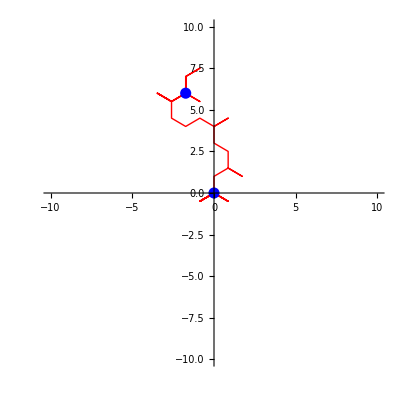

```mathematica
UnbiasedWalk=ListLinePlot[Table[Subscript[P, k],{k,0,40}],AspectRatio->Automatic, PlotRange->{{-10,10},{-10,10}}, PlotStyle->{Thick, Red}];
Endpoints=Graphics[{{Blue, PointSize[0.02],Point[Subscript[P, 0]]},
{Blue, PointSize[0.02],Point[Subscript[P, 40]]}}];
Show[{UnbiasedWalk, Endpoints}]
```

### Modulated hexagonal walk

-Graphics-

```mathematica
Clear[wr, wb]
```

```mathematica
wr[x_]:={1/4,2/3+1/2 Cos[(2π)/5 x],2/3-1/2 Cos[(2π)/5 x]}
wb[x_]:={0,2/3-1/2 Cos[(2π)/5 x],2/3+1/2 Cos[(2π)/5 x]}
```

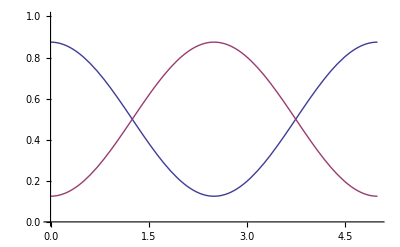

```mathematica
Plot[{(2/3+1/2 Cos[(2π)/5 x])/(4/3),(2/3-1/2 Cos[(2π)/5 x])/(4/3)},{x,0,5},PlotRange->{0,1}]
```

```mathematica
wr[x_]:={1/6,2/3+1/2 Cos[(2π)/5 x],2/3-1/2 Cos[(2π)/5 x]}
wb[x_]:={0,2/3-1/2 Cos[(2π)/5 x],2/3+1/2 Cos[(2π)/5 x]}
```

```mathematica
wr[x]
wb[x]
```

{1/6,2/3+1/2 Cos[(2 π x)/5],2/3-1/2 Cos[(2 π x)/5]}

{0,2/3-1/2 Cos[(2 π x)/5],2/3+1/2 Cos[(2 π x)/5]}

```mathematica
wr[x_]:={1,1,1}
wb[x_]:={1,1,1}
```

```mathematica
Clear[P]
```

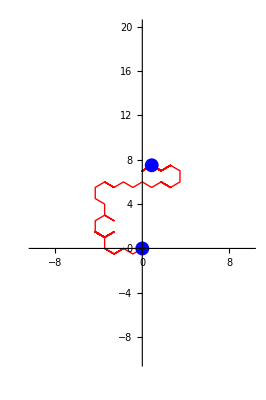

```mathematica
Subscript[P, 0]={0,0};
Subscript[P, 1]=RandomChoice[wr[Subscript[P, 0]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 0];
Subscript[P, 2]=RandomChoice[wb[Subscript[P, 1]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 1];
Subscript[P, 3]=RandomChoice[wr[Subscript[P, 2]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 2];
Subscript[P, 4]=RandomChoice[wb[Subscript[P, 3]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 3];
Subscript[P, 5]=RandomChoice[wr[Subscript[P, 4]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 4];
Subscript[P, 6]=RandomChoice[wb[Subscript[P, 5]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 5];
Subscript[P, 7]=RandomChoice[wr[Subscript[P, 6]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 6];
Subscript[P, 8]=RandomChoice[wb[Subscript[P, 7]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 7];
Subscript[P, 9]=RandomChoice[wr[Subscript[P, 8]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 8];
Subscript[P, 10]=RandomChoice[wb[Subscript[P, 9]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 9];
Subscript[P, 11]=RandomChoice[wr[Subscript[P, 10]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 10];
Subscript[P, 12]=RandomChoice[wb[Subscript[P, 11]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 11];
Subscript[P, 13]=RandomChoice[wr[Subscript[P, 12]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 12];
Subscript[P, 14]=RandomChoice[wb[Subscript[P, 13]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 13];
Subscript[P, 15]=RandomChoice[wr[Subscript[P, 14]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 14];
Subscript[P, 16]=RandomChoice[wb[Subscript[P, 15]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 15];
Subscript[P, 17]=RandomChoice[wr[Subscript[P, 16]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 16];
Subscript[P, 18]=RandomChoice[wb[Subscript[P, 17]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 17];
Subscript[P, 19]=RandomChoice[wr[Subscript[P, 18]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 18];
Subscript[P, 20]=RandomChoice[wb[Subscript[P, 19]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 19];
Subscript[P, 21]=RandomChoice[wr[Subscript[P, 20]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 20];
Subscript[P, 22]=RandomChoice[wb[Subscript[P, 21]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 21];
Subscript[P, 23]=RandomChoice[wr[Subscript[P, 22]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 22];
Subscript[P, 24]=RandomChoice[wb[Subscript[P, 23]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 23];
Subscript[P, 25]=RandomChoice[wr[Subscript[P, 24]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 24];
Subscript[P, 26]=RandomChoice[wb[Subscript[P, 25]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 25];
Subscript[P, 27]=RandomChoice[wr[Subscript[P, 26]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 26];
Subscript[P, 28]=RandomChoice[wb[Subscript[P, 27]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 27];
Subscript[P, 29]=RandomChoice[wr[Subscript[P, 28]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 28];
Subscript[P, 30]=RandomChoice[wb[Subscript[P, 29]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 29];
Subscript[P, 31]=RandomChoice[wr[Subscript[P, 30]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 30];
Subscript[P, 32]=RandomChoice[wb[Subscript[P, 31]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 31];
Subscript[P, 33]=RandomChoice[wr[Subscript[P, 32]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 32];
Subscript[P, 34]=RandomChoice[wb[Subscript[P, 33]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 33];
Subscript[P, 35]=RandomChoice[wr[Subscript[P, 34]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 34];
Subscript[P, 36]=RandomChoice[wb[Subscript[P, 35]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 35];
Subscript[P, 37]=RandomChoice[wr[Subscript[P, 36]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 36];
Subscript[P, 38]=RandomChoice[wb[Subscript[P, 37]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 37];
Subscript[P, 39]=RandomChoice[wr[Subscript[P, 38]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 38];
Subscript[P, 40]=RandomChoice[wb[Subscript[P, 39]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 39];
Subscript[P, 41]=RandomChoice[wr[Subscript[P, 40]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 40];
Subscript[P, 42]=RandomChoice[wb[Subscript[P, 41]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 41];
Subscript[P, 43]=RandomChoice[wr[Subscript[P, 42]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 42];
Subscript[P, 44]=RandomChoice[wb[Subscript[P, 43]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 43];
Subscript[P, 45]=RandomChoice[wr[Subscript[P, 44]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 44];
Subscript[P, 46]=RandomChoice[wb[Subscript[P, 45]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 45];
Subscript[P, 47]=RandomChoice[wr[Subscript[P, 46]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 46];
Subscript[P, 48]=RandomChoice[wb[Subscript[P, 47]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 47];
Subscript[P, 49]=RandomChoice[wr[Subscript[P, 48]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 48];
Subscript[P, 50]=RandomChoice[wb[Subscript[P, 49]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 49];
Subscript[P, 51]=RandomChoice[wr[Subscript[P, 50]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 50];
Subscript[P, 52]=RandomChoice[wb[Subscript[P, 51]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 51];
Subscript[P, 53]=RandomChoice[wr[Subscript[P, 52]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 52];
Subscript[P, 54]=RandomChoice[wb[Subscript[P, 53]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 53];
Subscript[P, 55]=RandomChoice[wr[Subscript[P, 54]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 54];
Subscript[P, 56]=RandomChoice[wb[Subscript[P, 55]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 55];
Subscript[P, 57]=RandomChoice[wr[Subscript[P, 56]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 56];
Subscript[P, 58]=RandomChoice[wb[Subscript[P, 57]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 57];
Subscript[P, 59]=RandomChoice[wr[Subscript[P, 58]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 58];
Subscript[P, 60]=RandomChoice[wb[Subscript[P, 59]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 59];
Subscript[P, 61]=RandomChoice[wr[Subscript[P, 60]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 60];
Subscript[P, 62]=RandomChoice[wb[Subscript[P, 61]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 61];
Subscript[P, 63]=RandomChoice[wr[Subscript[P, 62]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 62];
Subscript[P, 64]=RandomChoice[wb[Subscript[P, 63]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 63];
Subscript[P, 65]=RandomChoice[wr[Subscript[P, 64]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 64];
Subscript[P, 66]=RandomChoice[wb[Subscript[P, 65]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 65];
Subscript[P, 67]=RandomChoice[wr[Subscript[P, 66]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 66];
Subscript[P, 68]=RandomChoice[wb[Subscript[P, 67]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 67];
Subscript[P, 69]=RandomChoice[wr[Subscript[P, 68]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 68];
Subscript[P, 70]=RandomChoice[wb[Subscript[P, 69]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 69];
Subscript[P, 71]=RandomChoice[wr[Subscript[P, 70]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 70];
Subscript[P, 72]=RandomChoice[wb[Subscript[P, 71]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 71];
Subscript[P, 73]=RandomChoice[wr[Subscript[P, 72]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 72];
Subscript[P, 74]=RandomChoice[wb[Subscript[P, 73]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 73];
Subscript[P, 75]=RandomChoice[wr[Subscript[P, 74]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 74];
Subscript[P, 76]=RandomChoice[wb[Subscript[P, 75]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 75];
Subscript[P, 77]=RandomChoice[wr[Subscript[P, 76]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 76];
Subscript[P, 78]=RandomChoice[wb[Subscript[P, 77]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 77];
Subscript[P, 79]=RandomChoice[wr[Subscript[P, 78]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 78];
Subscript[P, 80]=RandomChoice[wb[Subscript[P, 79]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 79];
Subscript[P, 81]=RandomChoice[wr[Subscript[P, 80]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 80];
Subscript[P, 82]=RandomChoice[wb[Subscript[P, 81]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 81];
Subscript[P, 83]=RandomChoice[wr[Subscript[P, 82]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 82];
Subscript[P, 84]=RandomChoice[wb[Subscript[P, 83]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 83];
Subscript[P, 85]=RandomChoice[wr[Subscript[P, 84]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 84];
Subscript[P, 86]=RandomChoice[wb[Subscript[P, 85]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 85];
Subscript[P, 87]=RandomChoice[wr[Subscript[P, 86]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 86];
Subscript[P, 88]=RandomChoice[wb[Subscript[P, 87]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 87];
Subscript[P, 89]=RandomChoice[wr[Subscript[P, 88]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 88];
Subscript[P, 90]=RandomChoice[wb[Subscript[P, 89]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 89];
Subscript[P, 91]=RandomChoice[wr[Subscript[P, 90]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 90];
Subscript[P, 92]=RandomChoice[wb[Subscript[P, 91]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 91];
Subscript[P, 93]=RandomChoice[wr[Subscript[P, 92]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 92];
Subscript[P, 94]=RandomChoice[wb[Subscript[P, 93]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 93];
Subscript[P, 95]=RandomChoice[wr[Subscript[P, 94]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 94];
Subscript[P, 96]=RandomChoice[wb[Subscript[P, 95]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 95];
Subscript[P, 97]=RandomChoice[wr[Subscript[P, 96]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 96];
Subscript[P, 98]=RandomChoice[wb[Subscript[P, 97]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 97];
Subscript[P, 99]=RandomChoice[wr[Subscript[P, 98]⟦1⟧]->{R1,R2,R3}]+Subscript[P, 98];
Subscript[P, 100]=RandomChoice[wb[Subscript[P, 99]⟦1⟧]->{B1,B2,B3}]+Subscript[P, 99];


ModulatedWalk=ListLinePlot[Table[Subscript[P, k],{k,0,100}],AspectRatio->Automatic, PlotRange->{{-10,10},{-10,20}}, PlotStyle->{Thick, Red}];
Endpoints=Graphics[{{Blue, PointSize[0.025],Point[Subscript[P, 0]]},
{Blue, PointSize[0.025],Point[Subscript[P, 100]]}}];
Show[{ModulatedWalk, Endpoints}]
```

```mathematica
wr[x_,y_]:={1/4,2/3+1/2 Cos[(2π)/5 x],2/3-1/2 Cos[(2π)/5 x]}
wb[x_,y_]:={0,2/3-1/2 Cos[(2π)/5 x],2/3+1/2 Cos[(2π)/5 x]}
```

```mathematica
wb[x,y]
```

{0,2/3-1/2 Cos[(2 π x)/5],2/3+1/2 Cos[(2 π x)/5]}

```mathematica
wr[x_,y_]:={1,1,1}
wb[x_,y_]:={1,1,1}
```

```mathematica
Subscript[P, 0]={0,0};
Subscript[P, 1]=RandomChoice[wr[Subscript[P, 0]⟦1⟧,Subscript[P, 0]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 0];
Subscript[P, 2]=RandomChoice[wb[Subscript[P, 1]⟦1⟧,Subscript[P, 1]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 1];
Subscript[P, 3]=RandomChoice[wr[Subscript[P, 2]⟦1⟧,Subscript[P, 2]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 2];
Subscript[P, 4]=RandomChoice[wb[Subscript[P, 3]⟦1⟧,Subscript[P, 3]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 3];
Subscript[P, 5]=RandomChoice[wr[Subscript[P, 4]⟦1⟧,Subscript[P, 4]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 4];
Subscript[P, 6]=RandomChoice[wb[Subscript[P, 5]⟦1⟧,Subscript[P, 5]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 5];
Subscript[P, 7]=RandomChoice[wr[Subscript[P, 6]⟦1⟧,Subscript[P, 6]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 6];
Subscript[P, 8]=RandomChoice[wb[Subscript[P, 7]⟦1⟧,Subscript[P, 7]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 7];
Subscript[P, 9]=RandomChoice[wr[Subscript[P, 8]⟦1⟧,Subscript[P, 8]⟦2⟧]->{R1,R2,R3}]+Subscript[P, 8];
Subscript[P, 10]=RandomChoice[wb[Subscript[P, 9]⟦1⟧,Subscript[P, 9]⟦2⟧]->{B1,B2,B3}]+Subscript[P, 9];
```

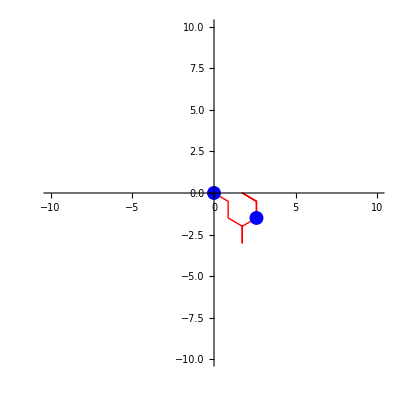

```mathematica
ModulatedWalk=ListLinePlot[Table[Subscript[P, k],{k,0,10}],AspectRatio->Automatic, PlotRange->{{-10,10},{-10,10}}, PlotStyle->{Thick, Red}];
Endpoints=Graphics[{{Blue, PointSize[0.025],Point[Subscript[P, 0]]},
{Blue, PointSize[0.025],Point[Subscript[P, 10]]}}];
Show[{ModulatedWalk, Endpoints}]
```

```mathematica
P[0]={0,0};
P[k_]:=Which[Mod[k,2]==1,RandomChoice[wr[P[k-1]⟦1⟧,P[k-1]⟦2⟧]->{R1, R2, R3}]+P[k-1],Mod[k,2]==0,RandomChoice[wb[P[k-1]⟦1⟧,P[k-1]⟦2⟧]->{B1,B2, B3}]+P[k-1]]
```

```mathematica
P[1]
```

{-0.866025,-0.5}

```mathematica
P[2]
```

{1.73205,0.}

```mathematica
Table[P[k],{k,0,10}]
```

{{0,0},{0.866025,-0.5},{1.73205,0.},{2.59808,-0.5},{0.,0.},{0.866025,-0.5},{0.,0.},{2.59808,-0.5},{0.,0.},{0.866025,-0.5},{0.,0.}}

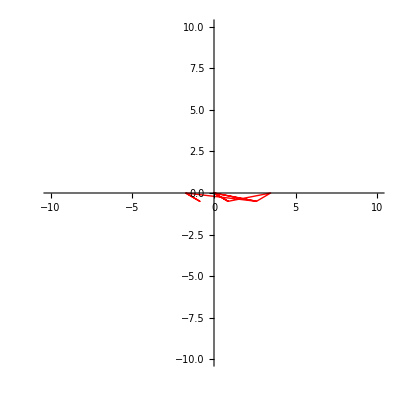

```mathematica
ListLinePlot[{P[0],P[1],P[2],P[3],P[4],P[5],P[6],P[7],P[8],P[9],P[10]},AspectRatio->Automatic, PlotRange->{{-10,10},{-10,10}}, PlotStyle->{Thick, Red}]
```

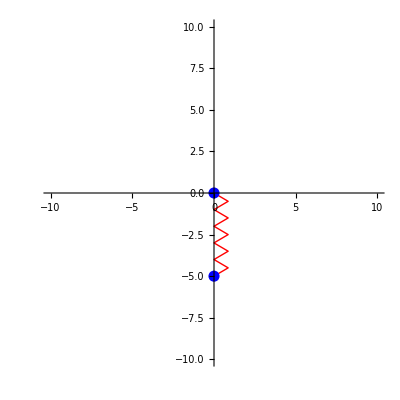

```mathematica
ModulatedWalk=ListLinePlot[Table[Subscript[P, k],{k,0,10}],AspectRatio->Automatic, PlotRange->{{-10,10},{-10,10}}, PlotStyle->{Thick, Red}];
Endpoints=Graphics[{{Blue, PointSize[0.02],Point[Subscript[P, 0]]},
{Blue, PointSize[0.02],Point[Subscript[P, 10]]}}];
Show[{ModulatedWalk, Endpoints}]
```

```mathematica
Table[Subscript[P, k],{k,0,5}]
```

{{0,0},{0.866025,-0.5},{1.73205,0.},{2.59808,-0.5},{1.73205,0.},{0.866025,-0.5}}

```mathematica
Subscript[P, 0]={0,0};
Subscript[P, 1]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 0]];
Subscript[P, 2]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 1]];
Subscript[P, 3]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 2]];
Subscript[P, 4]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 3]];
Subscript[P, 5]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 4]];
Subscript[P, 6]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 5]];
Subscript[P, 7]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 6]];
Subscript[P, 8]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 7]];
Subscript[P, 9]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 8]];
Subscript[P, 10]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 9]];
Subscript[P, 11]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 10]];
Subscript[P, 12]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 11]];
Subscript[P, 13]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 12]];
Subscript[P, 14]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 13]];
Subscript[P, 15]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 14]];
Subscript[P, 16]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 15]];
Subscript[P, 17]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 16]];
Subscript[P, 18]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 17]];
Subscript[P, 19]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 18]];
Subscript[P, 20]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 19]];
Subscript[P, 21]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 20]];
Subscript[P, 22]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 21]];
Subscript[P, 23]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 22]];
Subscript[P, 24]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 23]];
Subscript[P, 25]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 24]];
Subscript[P, 26]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 25]];
Subscript[P, 27]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 26]];
Subscript[P, 28]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 27]];
Subscript[P, 29]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 28]];
Subscript[P, 30]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 29]];
Subscript[P, 31]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 30]];
Subscript[P, 32]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 31]];
Subscript[P, 33]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 32]];
Subscript[P, 34]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 33]];
Subscript[P, 35]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 34]];
Subscript[P, 36]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 35]];
Subscript[P, 37]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 36]];
Subscript[P, 38]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 37]];
Subscript[P, 39]=Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],Subscript[P, 38]];
Subscript[P, 40]=Apply[Function[RandomChoice[wb[#1,#2]->{B1,B2,B3}]+{#1,#2}],Subscript[P, 39]];
```

```mathematica
ModulatedWalk=ListLinePlot[Table[Subscript[P, k],{k,0,40}],AspectRatio->Automatic, PlotRange->{{-10,10},{-10,10}}, PlotStyle->{Thick, Red}];
Endpoints=Graphics[{{Blue, PointSize[0.02],Point[Subscript[P, 0]]},
{Blue, PointSize[0.02],Point[Subscript[P, 40]]}}];
Show[{ModulatedWalk, Endpoints}]
```

-Graphics-

```mathematica
wb[x,y]
```

{0,2/3-1/2 Cos[(2 π x)/5],2/3+1/2 Cos[(2 π x)/5]}

```mathematica
Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],{0,0}]
```

{0.866025,-0.5}

```mathematica
Table[Apply[Function[RandomChoice[wr[#1,#2]->{R1,R2,R3}]+{#1,#2}],{0,0}],{k,1,100}]
```

{{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{-0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{-0.866025,-0.5},{-0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{-0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{-0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{-0.866025,-0.5},{-0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{-0.866025,-0.5},{0.866025,-0.5},{-0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{-0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{-0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{-0.866025,-0.5},{0.866025,-0.5}}

```mathematica
Tally[%]
```

{{{0.866025,-0.5},88},{{-0.866025,-0.5},12}}

```mathematica
{0,2/3+1/2 Cos[(2π)/5 x],2/3-1/2 Cos[(2π)/5 x]}
```

```mathematica
Table[Apply[Function[RandomChoice[{0,2/3+1/2 Cos[(2π)/5#1],2/3-1/2 Cos[(2π)/5#1]}->{R1,R2,R3}]+{#1,#2}],{0,0}],{k,1,20}]
```

{{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{-0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5},{-0.866025,-0.5},{0.866025,-0.5},{0.866025,-0.5}}

```mathematica
{0,2/3+1/2 Cos[(2π)/5 0],2/3-1/2 Cos[(2π)/5 0]}
```

{0,7/6,1/6}